Examples for working with finite automata (deterministic, non-deterministic and epsilon)
by Tomás de Camino Beck

## Introduction

I have created a series of posts regarding finite state machines. On this post, I just show several examples of using Mathematica to evaluate finite state automata, either deterministic, non deterministic, or non-deterministic with epsilon transitions.

Most of these examples are textbook examples, meant for teaching purposes.

Here I use just a few functions to compute strings over a state machine definition, determine if a string is valid, and then give you some functions for displaying the graph and the transition table.

Most examples are taken from Hopcroft & Ullman, or Sipser’s book.

## Defining an Automata

For defining an automata we use associations.  Each transition function  is defines as an association <|key_1→val_1,key_2→val_2,…|>, where a key→val rule is defines as {state, "symbol"}→{state or states}.  Symbols are declared as characters (except for empty symbol ϵ).  Look carefully at the examples to get a good idea on how to define automata transitions.

## Basic Functions

### Finite Automata Computation

```mathematica
Closure[δ_,state_List]:=Union[Map[Flatten[Most[NestWhileList[Union@@Table[δ[{#1[[i]],ϵ}]/._Missing->{},{i,Length[#1]}]&,{#},#≠ {}&]/._Missing->{}]]&,state]//Flatten]
DeltaHat[δ_,q0_List,string_]:=FoldList[Closure[δ,Union@@Table[δ[{#1[[i]],#2}]/._Missing->Nothing,{i,Length[#1]}]]&,Closure[δ,q0],Characters[string]]
IsValidQ[δ_,q0_List,qf_List,string_]:=ContainsAny[qf,Fold[Closure[δ,Union@@Table[δ[{#1[[i]],#2}]/._Missing->Nothing,{i,Length[#1]}]]&,Closure[δ,q0],Characters[string]]]
```

#### Usage

DeltaHat[association, {initial_state}, string]

Computes string using the transitions defined by association starting from initial_state.  Returns the states reached for each character in string (from left to right)

IsValidQ[association, {initial_states}, {final_states},string]

Computes string using the transitions defined by association starting from initial_state.  true or false if any of the final_states are reached

### Graph Creation

```mathematica
ShowGraphFA[edges_,states_List,q0_,q_List,edgelabels_,opts___]:=Graph[
edges,
VertexSize->0.25,
VertexLabels->Placed["Name",Center],
VertexStyle->Join[{0->White},Map[(#->Red)&,q]],
EdgeWeight->edgelabels,
EdgeLabels->"EdgeWeight",
opts
]
```

#### Usage

ShowGraphFA[edges, states,{ initial_states}, {final_states},{edge_labels}]

Shows a graph with directed edges.  initial_states are drawn white, final_states are red. edge_labels have to be specified in the same order as the edges

### Transition Table

```mathematica
FATable[δ_,states_,Σ_,opts___]:=Grid[
Join[List/@Prepend[states,"Q\Σ"],Prepend[Partition[Flatten[Outer[δ[{#1,#2}]/._Missing->"-"&,states,Σ,1],1],Length[Σ]],Σ],2],
Alignment->Center,
Spacings->{2,1},
Frame->All,
ItemStyle->"Text",
Background->{{Gray,None},{LightGray,None}},
opts
]
```

#### Usage

FATable[association, states_list ,alphabet_list]

Creates a transition table for the automata defined with association, using the states_list, with symbols from the alphabet_list

## Example 1

Strings Accepted: This automata accepts   (Example taken from Sipser’s book).  Start state 0,  final states {1,3}

Definition:

```mathematica
δ=Association[
{0,ϵ}->{1,3},
{1,"a"}->{2},
{2,"a"}->{1},
{3,"a"}->{4},
{4,"a"}->{5},
{5,"a"}->{3}
];
```

Graph :

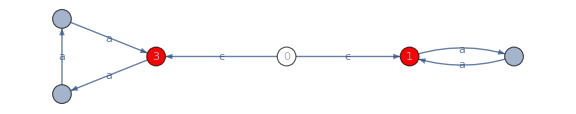

```mathematica
ShowGraphFA[{0->1,0->3,1->2,2->1,3->4,4->5,5->3},{0,1,2,3,4,5},{0},{1,3},{"ϵ","ϵ","a","a","a","a","a"},ImageSize->Large]
```

Transition Table:

```mathematica
FATable[δ,{0,1,2,3,4,5},{ϵ,"a"}]
```

Q\Σ | ϵ | a
0 | {1,3} | -
1 | - | {2}
2 | - | {1}
3 | - | {4}
4 | - | {5}
5 | - | {3}

Evaluation:

```mathematica
DeltaHat[δ,{0},"aaa"]
```

{{0,1,3},{2,4},{1,5},{2,3}}

```mathematica
IsValidQ[δ,{0},{1,3},"aaa"]
```

True

## Example 2

Strings Accepted: Accepts strings that start and finish with “a”, or start and finish with “b”. Starting state 0, final states {1,3}

Definition:

```mathematica
δ=Association[
{0,"a"}->{1},
{0,"b"}->{3},
{1,"a"}->{1},
{1,"b"}->{2},
{2,"b"}->{2},
{2,"a"}->{1},
{3,"b"}->{3},
{3,"a"}->{4},
{4,"b"}->{3},
{4,"a"}->{4}
];
```

Graph :

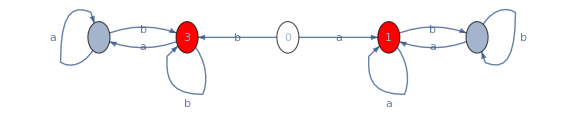

```mathematica
ShowGraphFA[{0->1,0->3,1->1,1->2,2->2,2->1,3->3,3->4,4->3,4->4},{0,1,2,3,4,5},{0},{1,3},{"a","b","a","b","b","a","b","a","b","a"},ImageSize->Large]
```

Transition Table:

```mathematica
FATable[δ,{0,1,2,3,4},{"a","b"}]
```

Q\Σ | a | b
0 | {1} | {3}
1 | {1} | {2}
2 | {1} | {2}
3 | {4} | {3}
4 | {4} | {3}

Evaluation:

```mathematica
DeltaHat[δ,{0},"abb"]
```

{{0},{1},{2},{2}}

```mathematica
IsValidQ[δ,{0},{1,3},"abb"]
```

```mathematica
DeltaHat[δ,{0},"abba"]
```

{{0},{1},{2},{2},{1}}

```mathematica
IsValidQ[δ,{0},{1,3},"abba"]
```

True

## Example 3

### Strings Accepted

Accepts strings that end in 1. initial state 0, final state 1

### Definition

```mathematica
δ=Association[
{0,"0"}->{0},
{0,"1"}->{1},
{1,"0"}->{0},
{1,"1"}->{1}
];
```

### Graph

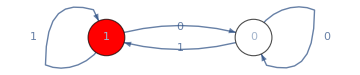

```mathematica
ShowGraphFA[{0->0,0->1,1->0,1->1},{0,1},{0},{1},{"0","1","0","1"},ImageSize->Medium]
```

### Transition Table

```mathematica
FATable[δ,{0,1},{"0","1"}]
```

Q\Σ | 0 | 1
0 | {0} | {1}
1 | {0} | {1}

### Evaluation

```mathematica
DeltaHat[δ,{0},"01001"]
```

{{0},{0},{1},{0},{0},{1}}

```mathematica
IsValidQ[δ,{0},{1},"01001"]
```

True

## Example 4

Strings Accepted:  Accepts binary strings that are integers multiples of 4 in binary notation. Starting state 0, final state 0

```mathematica
δ=Association[
{0,"0"}->{0},
{0,"1"}->{2},
{1,"0"}->{0},
{1,"1"}->{2},
{2,"0"}->{1},
{2,"1"}->{2}
];
```

Graph :

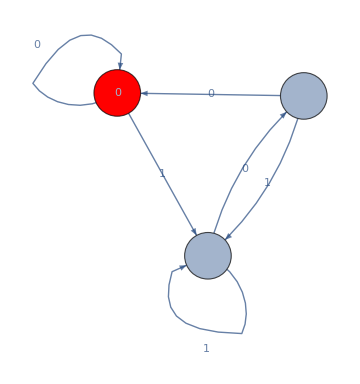

```mathematica
ShowGraphFA[{0->0,0->2,1->0,1->2,2->1,2->2},{0,1,2},{0},{0},{"0","1","0","1","0","1"},ImageSize->Medium]
```

Transition Table:

```mathematica
FATable[δ,{0,1,2},{"0","1"}]
```

Q\Σ | 0 | 1
0 | {0} | {2}
1 | {0} | {2}
2 | {1} | {2}

Evaluation:

```mathematica
DeltaHat[δ,{0},"01001"]
```

{{0},{0},{2},{1},{0},{2}}

```mathematica
IsValidQ[δ,{0},{0},"1100"]
```

True

## Example 5

### Strings Accepted:

Contains at least one 1 and a pair number of 0 after the last 1.

### Definition:

```mathematica
δ=Association[
{0,"0"}->{0},
{0,"1"}->{1},
{1,"0"}->{2},
{1,"1"}->{1},
{2,"0"}->{1},
{2,"1"}->{1}
];
```

### Graph :

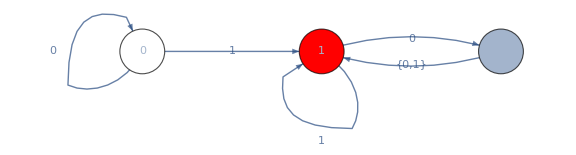

```mathematica
ShowGraphFA[{0->0,0->1,1->2,1->1,2->1},{0,1,2},{0},{1},{"0","1","0","1","{0,1}"},ImageSize->Large]
```

### Transition Table:

```mathematica
FATable[δ,{0,1,2},{"0","1"}]
```

Q\Σ | 0 | 1
0 | {0} | {1}
1 | {2} | {1}
2 | {1} | {1}

### Evaluation:

```mathematica
DeltaHat[δ,{0},"0100"]
```

{{0},{0},{1},{2},{1}}

```mathematica
IsValidQ[δ,{0},{1,3},"0100"]
```

True

## Example 6

### Strings Accepted:

Accepts decimal numbers with an optional  “+“ or “-“, followed by a sequence of integers digits, a point and another sequence of integer digits. The initial state is 0 and the final state 5.

### Definition:

```mathematica
δ=Association[
{0,ϵ}->{1},
{0,"+"}->{1},
{0,"-"}->{1},
{1,"0"}->{1,4},
{1,"1"}->{1,4},
{1,"2"}->{1,4},
{1,"3"}->{1,4},
{1,"4"}->{1,4},
{1,"5"}->{1,4},
{1,"6"}->{1,4},
{1,"7"}->{1,4},
{1,"8"}->{1,4},
{1,"9"}->{1,4},
{1,"."}->{2},
{2,"0"}->{3},
{2,"1"}->{3},
{2,"2"}->{3},
{2,"3"}->{3},
{2,"4"}->{3},
{2,"5"}->{3},
{2,"6"}->{3},
{2,"7"}->{3},
{2,"8"}->{3},
{2,"9"}->{3},
{4,"."}->{3},
{3,"0"}->{3},
{3,"1"}->{3},
{3,"2"}->{3},
{3,"3"}->{3},
{3,"4"}->{3},
{3,"5"}->{3},
{3,"6"}->{3},
{3,"7"}->{3},
{3,"8"}->{3},
{3,"9"}->{3},
{3,ϵ}->{5}
];
```

### Graph :

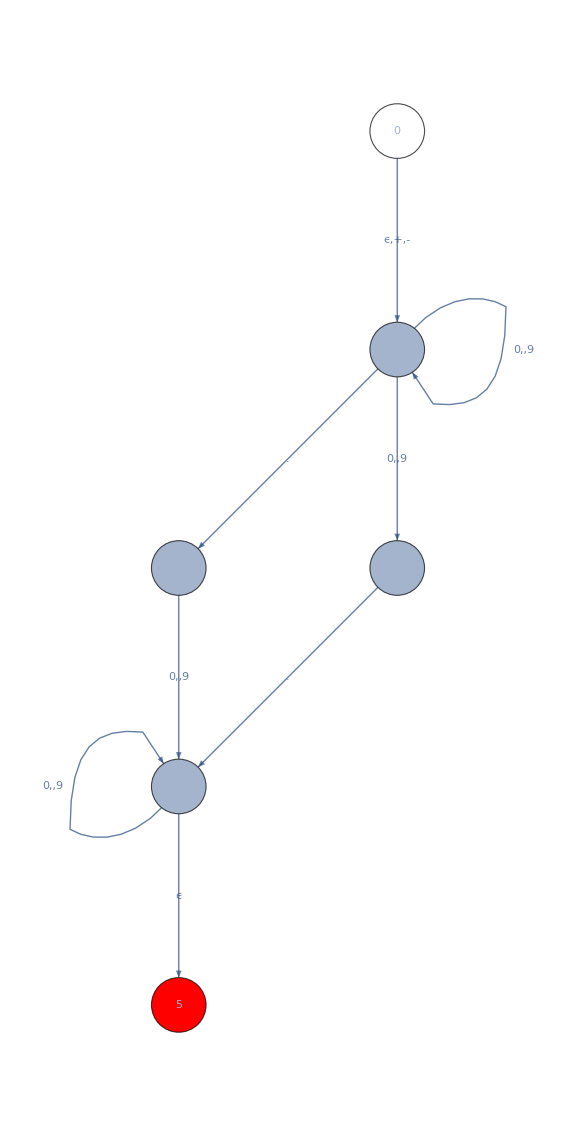

```mathematica
ShowGraphFA[{0->1,1->1,1->2,1->4,2->3,4->3,3->3,3->5},{0,1,2,3,4,5},{0},{5},{"ϵ,+,-","0,,9",".","0,,9","0,,9",".","0,,9","ϵ"},ImageSize->Large]
```

### Transition Table:

```mathematica
FATable[δ,{0,1,2,3,4,5},{ϵ,"+","-",".","0","1","2","3","4","5","6","7","8","9"}]
```

Q\Σ | ϵ | + | - | . | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
0 | {1} | {1} | {1} | - | - | - | - | - | - | - | - | - | - | -
1 | - | - | - | {2} | {1,4} | {1,4} | {1,4} | {1,4} | {1,4} | {1,4} | {1,4} | {1,4} | {1,4} | {1,4}
2 | - | - | - | - | {3} | {3} | {3} | {3} | {3} | {3} | {3} | {3} | {3} | {3}
3 | {5} | - | - | - | {3} | {3} | {3} | {3} | {3} | {3} | {3} | {3} | {3} | {3}
4 | - | - | - | {3} | - | - | - | - | - | - | - | - | - | -
5 | - | - | - | - | - | - | - | - | - | - | - | - | - | -

### Evaluation:

```mathematica
DeltaHat[δ,{0},"2.5"]
```

{{0,1},{1,4},{2,3,5},{3,5}}

```mathematica
DeltaHat[δ,{0},"+2.5"]
```

{{0,1},{1},{1,4},{2,3,5},{3,5}}

```mathematica
DeltaHat[δ,{0},"-55.6"]
```

{{0,1},{1},{1,4},{1,4},{2,3,5},{3,5}}

```mathematica
DeltaHat[δ,{0},"0.9129391"]
```

{{0,1},{1,4},{2,3,5},{3,5},{3,5},{3,5},{3,5},{3,5},{3,5},{3,5}}

```mathematica
DeltaHat[δ,{0},"5.4.6"]
```

{{0,1},{1,4},{2,3,5},{3,5},{},{}}

```mathematica
IsValidQ[δ,{0},{5},"0.9129391"]
```

True

```mathematica
IsValidQ[δ,{0},{5},"0.91.91"]
```

False

## Example 7

### Strings Accepted:

Accepts expressions that contain “ebay” or “web”. Initial state 0, final states {3,7} . The alphabet is all small English letters and space.

### Definition:

```mathematica
δ=Association[
{0," "}->{0},
{0,"a"}->{0},
{0,"b"}->{0},
{0,"c"}->{0},
{0,"d"}->{0},
{0,"e"}->{0,4},
{0,"f"}->{0},
{0,"g"}->{0},
{0,"h"}->{0},
{0,"i"}->{0},
{0,"j"}->{0},
{0,"k"}->{0},
{0,"l"}->{0},
{0,"m"}->{0},
{0,"n"}->{0},
{0,"o"}->{0},
{0,"p"}->{0},
{0,"q"}->{0},
{0,"r"}->{0},
{0,"s"}->{0},
{0,"t"}->{0},
{0,"u"}->{0},
{0,"v"}->{0},
{0,"w"}->{0,1},
{0,"x"}->{0},
{0,"y"}->{0},
{0,"z"}->{0},
{1,"e"}->{2},
{2,"b"}->{3},
{4,"b"}->{5},
{5,"a"}->{6},
{6,"y"}->{7}
];
```

### Graph :

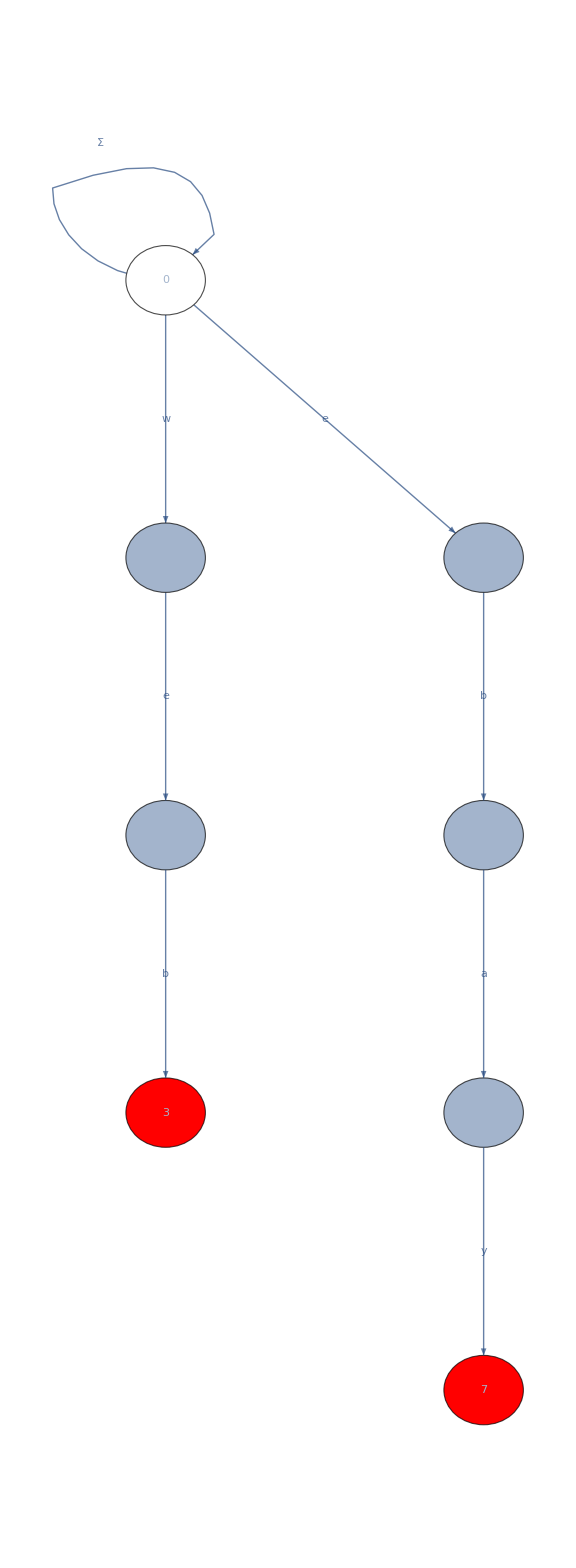

```mathematica
ShowGraphFA[{0->0,0->1,0->4,1->2,2->3,4->5,5->6,6->7},{0,1,2,3,4,5,6,7},{0},{3,7},{"Σ","w","e","e","b","b","a","y"},ImageSize->Large]
```

### Transition Table:

```mathematica
FATable[δ,{0,1,2,3,4,5,6,7},{" ","a","b","c","d","e","f","g","h","i","j","k","l","m","n","o","p","q","r","s","t","u","v","w","x","y","z"}]
```

Q\Σ |   | a | b | c | d | e | f | g | h | i | j | k | l | m | n | o | p | q | r | s | t | u | v | w | x | y | z
0 | {0} | {0} | {0} | {0} | {0} | {0,4} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0} | {0,1} | {0} | {0} | {0}
1 | - | - | - | - | - | {2} | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | -
2 | - | - | {3} | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | -
3 | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | -
4 | - | - | {5} | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | -
5 | - | {6} | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | -
6 | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | {7} | -
7 | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | - | -

### Evaluation:

```mathematica
DeltaHat[δ,{0},"as adebay"]
```

{{0},{0},{0},{0},{0},{0},{0,4},{0,5},{0,6},{0,7}}

```mathematica
DeltaHat[δ,{0},"as aday"]
```

{{0},{0},{0},{0},{0},{0},{0},{0}}

```mathematica
DeltaHat[δ,{0},"this is ebay"]
```

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0,4},{0,5},{0,6},{0,7}}

```mathematica
DeltaHat[δ,{0},"on the web"]
```

{{0},{0},{0},{0},{0},{0},{0,4},{0},{0,1},{0,2,4},{0,3,5}}

```mathematica
IsValidQ[δ,{0},{3,7},"on the web"]
```

True

```mathematica
IsValidQ[δ,{0},{3,7},"not here"]
```

False

## Example 8

### Strings Accepted:

Accepts a sum of symbols 0 Modulo 3. “r” resets de count to 0. Star state is 0, final state is 0

### Definition:

```mathematica
δ=Association[
{0,"0"}->{0},
{0,"r"}->{0},
{0,"1"}->{1},
{0,"2"}->{2},
{1,"0"}->{1},
{1,"2"}->{0},
{1,"r"}->{0},
{1,"1"}->{2},
{2,"0"}->{2},
{2,"1"}->{0},
{2,"r"}->{0},
{2,"2"}->{1}
];
```

### Graph :

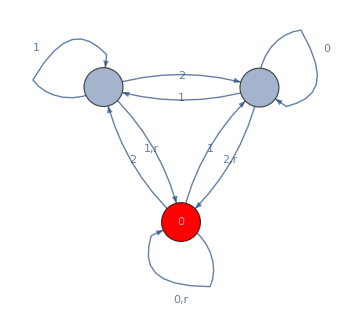

```mathematica
ShowGraphFA[{0->0,0->1,0->2,1->0,1->1,1->2,2->0,2->1,2->2},{0,1,2},{0},{0},{"0,r","1","2","2,r","0","1","1,r","2","1"},ImageSize->Medium]
```

### Transition Table:

```mathematica
FATable[δ,{0,1,2},{"r","0","1","2"}]
```

Q\Σ | r | 0 | 1 | 2
0 | {0} | {0} | {1} | {2}
1 | {0} | {1} | {2} | {0}
2 | {0} | {2} | {0} | {1}

### Evaluation:

```mathematica
DeltaHat[δ,{0},"10r22r012"]
```

{{0},{1},{1},{0},{2},{1},{0},{0},{1},{0}}

```mathematica
IsValidQ[δ,{0},{0},"10r22r012"]
```

True

## Example 9

### Strings Accepted:

Accepts strings that contain a sequence “001”. Start state 0, final state 3.

### Definition:

```mathematica
δ=Association[
{0,"1"}->{0},
{0,"0"}->{1},
{1,"1"}->{0},
{1,"0"}->{2},
{2,"0"}->{2},
{2,"1"}->{3},
{3,"0"}->{3},
{3,"1"}->{3}
];
```

### Graph :

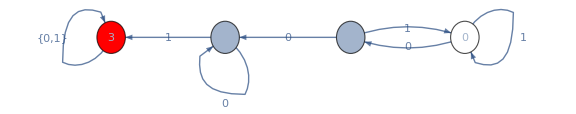

```mathematica
ShowGraphFA[{0->0,0->1,1->0,1->2,2->2,2->3,3->3},{0,1,2,3},{0},{3},{"1","0","1","0","0","1","{0,1}"},ImageSize->Large]
```

### Transition Table:

```mathematica
FATable[δ,{0,1,2,3},{"0","1"}]
```

Q\Σ | 0 | 1
0 | {1} | {0}
1 | {2} | {0}
2 | {2} | {3}
3 | {3} | {3}

### Evaluation:

```mathematica
DeltaHat[δ,{0},"0010"]
```

{{0},{1},{2},{3},{3}}

```mathematica
DeltaHat[δ,{0},"0100"]
```

{{0},{1},{0},{1},{2}}

```mathematica
IsValidQ[δ,{0},{3},"0010"]
```

True

## References

Hopcroft and Ullman, Introduction to Automata Theory, Languages and Computation, Addison Wesley.

Michael Sipser, Introduction to theTheory of Computation. PWS Publishing Company, 2006.